## Figure 1

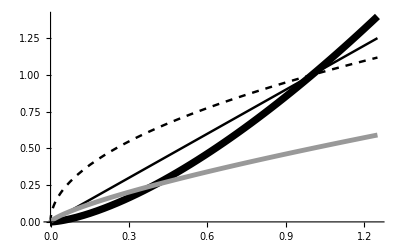

```mathematica
ps1= {{Dashed,Black,AbsoluteThickness[th]},{Black,AbsoluteThickness[th]},{Black,AbsoluteThickness[3 th]},{GrayLevel[gl],AbsoluteThickness[2th]}};(*{{Black, AbsoluteThickness[th-1]},{Black,AbsoluteThickness[th]},{Black,AbsoluteThickness[th+1]}, {Gray},{Gray,AbsoluteThickness[th+1]}};
*)
fig1= Plot[{z^0.5,z,z^1.5, z^0.75/2},{z,0,1.25},PlotStyle->ps1,AxesStyle->as,PlotRangePadding->None]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\final_energy_budget\\energy_budget\\ms_fig\\fig1.pdf",fig1]
```

C:\Users\tramiada\Documents\Projects\final_energy_budget\energy_budget\ms_fig\fig1.pdf

## Main code

```mathematica
On[Assert];

(*Position of the sun in the sky as a function of day of the year, time of the day, and latitude at longitude = 0*)
SolarRadiation[J_,t_,ϕ_]:= Module[{result,S0=1.361,sinδ,δ,cosδ, cosψ,sol,trise,tset,tt, DtoR = π/180,hs},
sinδ = 0.39785 Sin[(278.97 + 0.9856 J + 1.9165 Sin[(356.6 + 0.9856 J)DtoR])DtoR];
(*this is solar declination*)
δ = ArcSin[sinδ];
cosδ = Cos[δ];
cosψ[ti_]:=Sin[ϕ DtoR]sinδ + Cos[ϕ DtoR] cosδ Cos[(15.(ti-12))DtoR];

hs[δ_]:= ArcCos[(0 - Sin[ϕ DtoR]sinδ)/(Cos[ϕ DtoR] cosδ)]1/DtoR; 
(*cosψ disapears because we use geometric sunset*)
trise = 12- hs[δ]/15;
tset = 12 + hs[δ]/15;

If[t< trise || t > tset, 
result = 0,
result = S0 cosψ[t];
];
result *= 1000;
result];

(*Position of the sun in the sky as a function of day of the year, time of the day, and latitude at longitude = 0*)
SunRise[J_,ϕ_]:= Module[{result,sinδ,δ,cosδ, cosψ,sol,trise,tset,tt, DtoR = π/180,hs},
sinδ = 0.39785 Sin[(278.97 + 0.9856 J + 1.9165 Sin[(356.6 + 0.9856 J)DtoR])DtoR];
(*this is solar declination*)
δ = ArcSin[sinδ];
cosδ = Cos[δ];

hs[δ_]:= ArcCos[(0 - Sin[ϕ DtoR]sinδ)/(Cos[ϕ DtoR] cosδ)]1/DtoR; 
(*cosψ disapears because we use geometric sunset*)
trise = 12- hs[δ]/15;
result= Re@trise;
result];

(*Fixed constant and solar radiation function *)
day = 72; lat = 30 ;
trise = SunRise[day,lat];ZZ= {0.01,0.1,1,5};

(* data for solar radiation *)
predata = Table[{t, SolarRadiation[day,t,lat]},{t, trise,trise+12,12/10}];
SR = Interpolation[predata];
```

```mathematica
(*CONSTANTS AND SIMPLE FUNCTIONS USED*)

Ek =  7541; (*This is the ratio between E and k*)
c0= 28.; (*ref Bartholomew and Casey 1977*)
c1 = 1.5;
cz = 0.5;

(*Convection*)
cp =29.3; (*J/ mol K*)
wind = 1; (*m/s*)
(*original data tissue density:
1 kg /l =  1 kg/dm^3 = 1000g/dm^3 = 1000 g/ 10^(-3) m^3  = 1 10^6 g/m^3
*)
δ = 0.15 10^(6);(*measurement gives the 0.15. g/m^3*)
Ksth =0.05* cp (*this is tissue conductance. A sleeping bag has 0.05 (ex #6.4, mol / m2 s * J / mol K = J/m2 s K *);

s = 3.3472 ;(*specific heat capacity, 0.8 cal /g C = 0.8*4.184 J/g C*)
σ=5.67 10^(-8);(*W/m2 K4 = J / m2 s K*)
e = 0.04184;(*energy per contraction: 0.01 cal/g = 0.01*4.184 j/g*)

rK1 = 1; (* Coefficient for the conductance between the thorax and the rest of the body *)
rK2 = 1; (* Coefficient for the convection between the thorax and the environment *)
free = 0; (* Binary value 0 or 1 where there is free convection or laminar convection*)

Kv[z_]:= cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (* J/mol K x mol /m2 s = J / m2 K s*);

aw = 0.25; (*something per second*)
f[T_]:= aw T;

(*Start from radius calculating it is easier *)
rad[z_]:= (3. z/(2 π δ))^(1/3);
ch = 1; (*ch is the proportion of the cap with respect to the radius. radius * ch gives the height*)
h[z_]:= rad[z]* ch; (*The height of the cap*) 

(*ratio between thoracic and total mass*)
(*fcz[z_] := ((1/(3 2)) π h[z]^2  (3 rad[z] - h[z]))/(2/3 π r^3);*)
fcz[z_] := ((1/4)  h[z]^2  (3 rad[z] - h[z]))/(rad[z]^3);

(*Total surface of the spherical cap = surface of the thorax*)
Ath[z_]:= π rad[z] h[z] +  2 rad[z]^2 ArcCos[(rad[z]- h[z])/rad[z]] - (rad[z]-h[z])Sqrt[2 rad[z] h[z] - h[z]^2](*the first part is divided by 2 because of half a sphere, from pytagorian the base is a = (h (2 r - h))^(1/2) note that *)

(*Total surface are of  rest *)
As[z_]:= ( 2 π rad[z]^2  -  π rad[z] h[z] )  +   π rad[z]^2 (* m2*);

(*function for changes in environmental temperature*)
fTemp[t_,trise_,Trise_,Tmax_]:= Module[{tmax,tset,Tnoon,Tset,cT = 0.5,result},

If[
Trise == Tmax,result = Trise;Goto["end"]
];
Assert[Tmax >Trise];

tmax = 12 + 0.5 (12 - trise);
tset = 12 + (12- trise);
Tnoon  = Trise - (Tmax- Trise)/(tmax - trise) trise+ (Tmax- Trise)/(tmax - trise) 12;
Tset = Tnoon + cT (Tmax - Tnoon);

result = 
Which[
trise≤ t< tmax,
 Trise - (Tmax- Trise)/(tmax - trise) trise+ (Tmax- Trise)/(tmax - trise) t,
tmax ≤ t< tset,
 Tmax - (Tset- Tmax)/(tset - tmax) tmax+ (Tset- Tmax)/(tset - tmax) t,
tset ≤ t< trise +24,
 Tset  - (Trise - Tset)/(trise +24  - tset) tset + (Trise - Tset)/(trise +24  - tset)t
];

Label["end"];

result];

(*this function solve the the change in thoracic (and surface) temperature and find the warm-up time *)
Wtime[z_, rK1_, rK2_,starttf_,endtf_,free_, trise_, Trise_, Tmax_,aw_]:= Module[{ ε= 0.95, r3 =0.5,sol, cz = fcz[z], T1 , xy,pos,result, activetemp = c0 + c1 z cz ,Temp, newendtf, yy,maxyy,t1,t2,yt1,yt2,tmid,ytmid},

Temp[t_]:= fTemp[t,trise,Trise, Trise + Tmax ]; (*Simplify the definition of changes in temperature*)

T1 = Temp[starttf];
Assert[NumericQ@T1 == True];
newendtf = Min[endtf,12  +  (12 -trise)];

If[T1 ≥ activetemp, result = 0.; Goto[end]];

sol = If[free == True,
NDSolve[
{ Tth'[t] == 1/(s cz z ) (aw * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz)z) *( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  0.05Max[0.,(Ts[t]- Temp[t/3600.])]^(1.25) (1/(z/δ))^(1/12) - σ ε (273 + Ts[t])^4 + σ ε (273 + Temp[t/3600.])^4 + r3  SR[t/3600.])) ,Tth[starttf*3600.]==Ts[starttf*3600.]==T1},{Tth,Ts},{t,starttf *3600., newendtf* 3600.}],
NDSolve[
{Tth'[t] == 1/(s cz z) (aw* cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz) z) * ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (Ts[t]- Temp[t/3600.]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Temp[t/3600.])^4 + r3 SR[t/3600.])) ,Tth[starttf*3600.]==Ts[starttf*3600.]==T1},{Tth,Ts},{t,starttf *3600.,newendtf *3600.}]
];


(* Compute all values *)
yy = Table[Evaluate[Re@Tth[t]/.sol],{t,starttf*3600,newendtf*3600,2}];
maxyy = Max[yy];

If[maxyy < activetemp,
result = endtf -starttf,
pos = Position[yy,maxyy][[1,1]];
t1 = starttf*3600;
t2 = t1 + 2(pos-1); (*The minus one occurs because imagine max is at starttf, time 2 because of discretization in yy*)
yt1 = Evaluate[Re@Tth[t1] /. sol][[1]] - activetemp;
yt2 = Evaluate[Re@Tth[t2] /. sol][[1]] -activetemp;
Assert[yt1*yt2 < 0];
While[Abs[yt1 -yt2] > 10^(-5),
tmid = t1 + (t2 -t1)/2;
ytmid = Evaluate[Re@Tth[tmid] /. sol][[1]] - activetemp;
If[ytmid < 0,
t1 = tmid;
yt1 = ytmid,
t2 = tmid;
yt2 = ytmid
];
];
result = (t1 + t2)/(2. 3600) - starttf;
];
Label[end];
result];
```

```mathematica
(*Functions for resting, active and foraging rate*)
(* Multiply by  3600 to convert from second to hour*)
(* The unit is  in Watt hour = joule/hour*)

(* Resting metabolic rate per hour*)
eb[z_, T_, a1_, b1_]:= 3600. a1 z^b1 Exp[(- Ek)/(T + 273.15)] 10^8; (*COMPARE WITH Niven JE,Scharlemann JP.Do insect metabolic rates at rest and during flight scale with body mass?Biology Letters.2005;1(3):346-349. doi:10.1098/rsbl.2005.0311. *)

(* Active metabolic rate*)
ea[z_, T_, a2_, b2_]:= 3600. a2 z^b2 Exp[(- Ek)/Max[c0  + c1 z cz, T + 273.15]] 10^8;

(* Foraging rate*)
eg[z_, a3_,b3_,ε_:16]:= ε a3 z^b3 10 ;  (* use this so that in 60 min they take about 10  times their body mass if b3 = 1, ε = 4 cal/g = 16 J/g*)
```

Those values are just to get thing within one range of magnitude. This now matches with the appendix data from 1 

278.93 * 10^(-3) * 20 //ScientificForm (* 300 mm3/O2 h x 10^(-3) ml x 20  (O2 5 x 4. to cal to joule)  *) 

(* this is in watt *)
eb[5.165,23,1,0.75]  //ScientificForm

Let us assume that an insect can not take more than 250 times its mass.
C. humectus hidalgoensis is has a mean of 0.18 g and move 1.19 g during 23 min = 23/60 = 0.38 hour , then

1	Niven JE, Scharlemann JP. Do insect metabolic rates at rest and during flight scale with body mass? Biology Letters. 2005;1(3):346-349. doi:10.1098/rsbl.2005.0311.

```mathematica
Eb[z_,trise_, Trise_, Tmax_, tstart_, tend_, abparam_]:= Module[{ tset,Tnoon, Tset,tstart1,tend1, tstart2, tend2, tstart3,tend3,I1, I2, I3, result1= 0, result2 = 0, result3 = 0,f1,f2,f3,a1 , b1 , tmax,cT = 0.5,result},

tmax = 12 + 0.5 (12 - trise);
tset = 12 + (12- trise);
Tnoon  = Trise - (Tmax- Trise)/(tmax - trise) trise+ (Tmax- Trise)/(tmax - trise) 12;
Tset = Tnoon + cT (Tmax - Tnoon);

a1 = abparam[[1]];
b1 = abparam[[2]];

(* Due to the piecewise nature of temperature I need to break it down into 3 pieces *)
Assert[tstart≥ trise];

I1 = IntervalIntersection[Interval[{trise, tmax}],Interval[{tstart,tend}]];
I2 =  IntervalIntersection[Interval[{tmax,tset}],Interval[{tstart,tend}] ];
I3 =  IntervalIntersection[Interval [{tset, trise +24}],Interval[{tstart,tend}] ];

If[Length[I1]≠ 0,
tstart1 = I1[[1,1]];
tend1 = I1[[1,2]];
];

If[Length[I2]≠ 0,
tstart2 = I2[[1,1]];
tend2 = I2[[1,2]];
];

If[Length[I3]≠ 0,
tstart3 = I3[[1,1]];
tend3 = I3[[1,2]];
];

f1 = Trise - (Tmax- Trise)/(tmax - trise) trise+ (Tmax- Trise)/(tmax - trise) # &;

If[tstart1< tend1,
result1 = NIntegrate[eb[z, f1[t],a1,b1],{t,tstart1, tend1}]
];

f2 = Tmax - (Tset- Tmax)/(tset - tmax) tmax+ (Tset- Tmax)/(tset - tmax) # &; 
If[tstart2< tend2,
result2 = NIntegrate[eb[z, f2[t],a1,b1],{t,tstart2, tend2}]
];

f3= Tset  - (Trise - Tset)/(trise +24  - tset) tset + (Trise - Tset)/(trise +24  - tset)# &;
If[tstart3< tend3,
result3 = NIntegrate[eb[z, f3[t],a1,b1],{t,tstart3, tend3}]
];

result = result1 + result2+ result3;

result];

Ea[z_,trise_, Trise_, Tmax_, tstart_, tend_,abparam_]:= Module[{tset,Tnoon, Tset,tstart1=0,tend1=0, tstart2=0, tend2=0, tstart3=0,tend3=0,I1, I2, I3, result1= 0, result2 = 0, result3 = 0,f1,f2,f3,a2 , b2, tmax,cT = 0.5,result},

tmax = 12 + 0.5 (12 - trise);
tset = 12 + (12- trise);
Tnoon  = Trise - (Tmax- Trise)/(tmax - trise) trise+ (Tmax- Trise)/(tmax - trise) 12;
Tset = Tnoon + cT (Tmax - Tnoon);

a2 = abparam[[1]];
b2 = abparam[[2]];


(* Due to the piecewise nature of temperature I need to break it down into 3 pieces *)
Assert[tstart≥ trise];
(* Due to the piecewise nature of temperature I need to break it down into 3 pieces *)
Assert[tstart≥ trise];

I1 = IntervalIntersection[Interval[{trise, tmax}],Interval[{tstart,tend}]];
I2 =  IntervalIntersection[Interval[{tmax,tset}],Interval[{tstart,tend}] ];
I3 =  IntervalIntersection[Interval [{tset, trise +24}],Interval[{tstart,tend}] ];

If[Length[I1]≠ 0,
tstart1 = I1[[1,1]];
tend1 = I1[[1,2]];
];

If[Length[I2]≠ 0,
tstart2 = I2[[1,1]];
tend2 = I2[[1,2]];
];

If[Length[I3]≠ 0,
tstart3 = I3[[1,1]];
tend3 = I3[[1,2]];
];

f1 = Trise - (Tmax- Trise)/(tmax - trise) trise+ (Tmax- Trise)/(tmax - trise) # &;

If[tstart1< tend1,
result1 = NIntegrate[ea[z, f1[t],a2,b2],{t,tstart1, tend1}]
];

f2 = Tmax - (Tset- Tmax)/(tset - tmax) tmax+ (Tset- Tmax)/(tset - tmax) # &; 
If[tstart2< tend2,
result2 = NIntegrate[ea[z, f2[t],a2,b2],{t,tstart2, tend2}]
];

f3= Tset  - (Trise - Tset)/(trise +24  - tset) tset + (Trise - Tset)/(trise +24  - tset)# &;
If[tstart3< tend3,
result3 = NIntegrate[ea[z, f3[t],a2,b2],{t,tstart3, tend3}]
];

result = result1 + result2+ result3;

result];

(*When resource is limiting, compute tstart and tend first*)
ftf[z_,RR_,a3_,b3_]:= RR/(a3 z^b3 10);

Eg[z_,ε_,tstart_,tend_,abparam_]:= Module[{a3, b3,result},
a3 = abparam[[1]];
b3= abparam[[2]];

result = (tend -tstart) eg[z,a3,b3, ε];
result];
```

```mathematica
(* Energy budget given time is limited *)
EnTime[z_,trise_, Trise_, Tmax_, ε_, starttf_, tf_, allabparam_,nowarmup_,free_,aw_]:= Module[{result =0., gain= 0., activity = 0.,rest = 0.,tstart1,tend1,tstart2,tend2, abparam1,abparam2,abparam3,finaltf, newstarttf, warmtime, rK1 = 1., rK2= 1.},

abparam1= allabparam[[{1,2}]];
abparam2= allabparam[[{3,4}]];
abparam3= allabparam[[{5,6}]];

(* Calculate the amount of time needed to warm-up, the subtract witht total foraging time tf *)
If[nowarmup==True,
warmtime=0.,
warmtime = Wtime[z, rK1,rK2, starttf,starttf+tf,free,trise,Trise,Tmax,aw];
Assert[NumericQ[warmtime]==True];
];

If[warmtime ≥ tf, 
result = - Eb[z,trise,Trise, Tmax, trise, trise+24,abparam1];Goto[here];
];

newstarttf = starttf + warmtime;

finaltf = Min[starttf + tf,trise+24] ;
Assert[trise ≤ starttf];

(*Total energy gained*)
gain = Eg[z, ε, newstarttf, finaltf, abparam3];

(*Total energy used for activity*)
activity = Ea[z,trise,Trise, Tmax, newstarttf,finaltf,abparam2];

(*Total energy for resting*)
If[trise == newstarttf, (*the individual will rest until the rest of the day after foraging*)
rest = Eb[z,trise,Trise, Tmax, finaltf, trise + 24 , abparam1], (* otherwise, it will rest until starttf *)
tstart1 = trise;
tend1 = newstarttf;
rest = Eb[z,trise,Trise, Tmax, tstart1, tend1,abparam1];
If[starttf +tf < trise + 24,
tstart2 = starttf + tf;
tend2 = trise + 24;
rest += Eb[z,trise,Trise, Tmax, tstart2, tend2,abparam1];
];
];
result = gain - activity - rest;

Label[here];(*If warm-up takes longer than total foraging time allowed tf *)

result];
```

```mathematica
(* Energy budget given time is limited *)
EnResource[z_,trise_, Trise_, Tmax_, ε_, starttf_, RR_, allabparam_,nowarmup_,free_,aw_]:= Module[{result =0., gain= 0., activity = 0.,rest = 0.,tstart1,tend1,tstart2,tend2, abparam1,abparam2,abparam3,finaltf, newstarttf, warmtime, rK1 = 1., rK2= 1., a3, b3,tf,maxres =50.},

abparam1= allabparam[[{1,2}]];
abparam2= allabparam[[{3,4}]];
abparam3= allabparam[[{5,6}]];

a3  = allabparam[[5]];
b3  = allabparam[[6]];

(*put a maximum value for total resource acquired*)
tf = Min[ftf[z,RR, a3,b3],ftf[z,z*maxres, a3,b3]];


(* Calculate the amount of time needed to warm-up, the subtract witht total foraging time tf *)
If[nowarmup==True,
warmtime=0.,
warmtime = Wtime[z, rK1,rK2, starttf,starttf+tf,free,trise,Trise,Tmax,aw];
Assert[NumericQ[warmtime]==True];
];

If[warmtime ≥ tf, 
result = - Eb[z,trise,Trise, Tmax, trise, trise+24,abparam1];Goto[here];
];

newstarttf = starttf + warmtime;

finaltf = Min[starttf + tf,trise+24] ;
Assert[trise ≤ starttf];

(*Total energy gained*)
gain = Eg[z, ε, newstarttf, finaltf, abparam3];

(*Total energy used for activity*)
activity = Ea[z,trise,Trise, Tmax, newstarttf,finaltf,abparam2];

(*Total energy for resting*)
If[trise == newstarttf, (*the individual will rest until the rest of the day after foraging*)
rest = Eb[z,trise,Trise, Tmax, finaltf, trise + 24 , abparam1], (* otherwise, it will rest until starttf *)
tstart1 = trise;
tend1 = newstarttf;
rest = Eb[z,trise,Trise, Tmax, tstart1, tend1,abparam1];
If[starttf +tf < trise + 24,
tstart2 = starttf + tf;
tend2 = trise + 24;
rest += Eb[z,trise,Trise, Tmax, tstart2, tend2,abparam1];
];
];
result = gain - activity - rest;

Label[here];(*If warm-up takes longer than total foraging time allowed tf *)

result];
```

## Figure 2

#### panels ABC

```mathematica
figrow1 = {}; 
Do[
ca2 = 20;b2 = 0.75;
a1 = 1; b1 = 0.75; a2 = ca2 a1;  a3 = 1; b3 = 1. ;
allabparam = {a1, b1, a2,b2, a3, b3};
AB= {{a1, b1, a2,b2, a3, 0.5},{a1, b1, a2,b2, a3, 0.8},{a1, b1, a2,b2, a3, 1.25}};
ε = 16;
cTmax = 0.;
nowarmup = True;
free = True;
aw = 0.;
Trise =15.;


f[z_,i_]:=EnResource[z, trise,Trise, Trise +cTmax,ε, trise,RR,AB[[i]], nowarmup,free ,aw];

nstep =100;
(*data1 = Table[Flatten@{temp,f[temp,1]},{temp,0,40,step}];*)
data2 = Table[Flatten@{z,f[z,1]},{z,0.001,5.,5/nstep}];
data3 = Table[Flatten@{z,f[z,2]},{z,0.001,5.,5/nstep}];
data4 = Table[Flatten@{z,f[z,3]},{z,0.001,5.,5/nstep}];

temp= ListLinePlot[{(*data1,*)data2,data3,data4},PlotRange->{{0,5},{0,All}},AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None(*,PlotLabel->"RR_"<>ToString@RR<>"_ca2_"<>ToString@ca2<>"_b2_"<>ToString@b2,LabelStyle->Directive[16,Black,"Arial"]*)];
AppendTo[figrow1,temp];
,{RR,{2.5,20,1000}}];
```

#### panels DEF

```mathematica
figrow2 = {}; 
Do[
ca2 = 39.5;b2 = 1.25; RR= 1000;
a1 = 1; b1 = 0.75; a2 = ca2 a1;  a3 = 1; b3 = 1. ;
allabparam = {a1, b1, a2,b2, a3, b3};
AB= {{a1, b1, a2,b2, a3, 0.5},{a1, b1, a2,b2, a3, 0.8},{a1, b1, a2,b2, a3, 1.25}};
ε =16;
cTmax = 0.;
nowarmup = True;
free = True;
aw = 0.;
(*Trise =15.;*)


f[z_,i_]:=EnResource[z, trise,Trise, Trise +cTmax,ε, trise,RR,AB[[i]], nowarmup,free ,aw];

nstep =100;
(*data1 = Table[Flatten@{temp,f[temp,1]},{temp,0,40,step}];*)
data2 = Table[Flatten@{z,f[z,1]},{z,0.001,5.,5/nstep}];
data3 = Table[Flatten@{z,f[z,2]},{z,0.001,5.,5/nstep}];
data4 = Table[Flatten@{z,f[z,3]},{z,0.001,5.,5/nstep}];

temp= ListLinePlot[{(*data1,*)data2,data3,data4},PlotRange->{{0,5},{0,All}},AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None(*,PlotLabel->"RR_"<>ToString@RR<>"_ca2_"<>ToString@ca2<>"_b2_"<>ToString@b2,LabelStyle->Directive[16,Black,"Arial"]*)];
AppendTo[figrow2,temp];
,{Trise,{5,15,25}}];
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\final_energy_budget\\energy_budget\\ms_fig\\fig2a.pdf",figrow1[[1]]];
Export["C:\\Users\\tramiada\\Documents\\Projects\\final_energy_budget\\energy_budget\\ms_fig\\fig2b.pdf",figrow1[[2]]];
Export["C:\\Users\\tramiada\\Documents\\Projects\\final_energy_budget\\energy_budget\\ms_fig\\fig2c.pdf",figrow1[[3]]];
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\final_energy_budget\\energy_budget\\ms_fig\\fig2d.pdf",figrow2[[1]]];
Export["C:\\Users\\tramiada\\Documents\\Projects\\final_energy_budget\\energy_budget\\ms_fig\\fig2e.pdf",figrow2[[2]]];
Export["C:\\Users\\tramiada\\Documents\\Projects\\final_energy_budget\\energy_budget\\ms_fig\\fig2f.pdf",figrow2[[3]]];
```

## Figure 3

### panel A

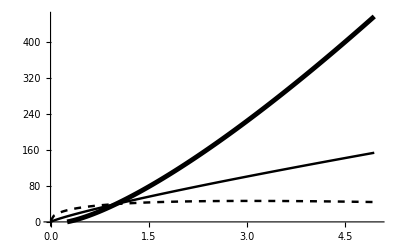

```mathematica
a1 = 1; b1 = 0.75; a2 = 5 a1; b2  = 0.75; 
allabparam = {a1, b1, a2,b2, a3, b3};
AB= {{a1, b1, a2,b2, a3, 0.5},{a1, b1, a2,b2, a3, 0.8},{a1, b1, a2,b2, a3, 1.25}};
ε = 16;
cTmax = 0.;
nowarmup = True;
free = True;
aw = 0.;
Trise =15.;
foragetime =0.5;

f[z_,i_]:=EnTime[z, trise,Trise, Trise +cTmax,ε, trise,foragetime,AB[[i]], nowarmup,free ,aw];

nstep = 100;
(*data1 = Table[Flatten@{temp,f[temp,1]},{temp,0,40,step}];*)
data2 = Table[Flatten@{z,f[z,1]},{z,0.001,5.,5/nstep}];
data3 = Table[Flatten@{z,f[z,2]},{z,0.001,5.,5/nstep}];
data4 = Table[Flatten@{z,f[z,3]},{z,0.001,5.,5/nstep}];

fig3a = ListLinePlot[{(*data1,*)data2,data3,data4},PlotRange->{{0,5},{0,All}},AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None]
```

### panle B

```mathematica
(*Plot figure 2a*)
B= 24;

Trise1 = 15;Trise2= 35; rho = 5;b1 = 0.75; b2 = 0.75; b3 = 0.5; a1 = 1.; a3 = 10.;

ten[z_,b2_,b3_, Trise_,tf_,ρ_]:= 3600((ρ a1)/a3 z^(b2-b3)  Exp[(- Ek)/Max[c0  + c1 z cz, Trise + 273.15]] 10^8+ a1/a3 z^(b1-b3) Exp[(- Ek)/(Trise + 273.15)] 10^8 (B/tf -1));
tden[z_,b2_,b3_, Trise_,tf_,ρ_]:= 3600((ρ a1)/a3 b2/b3 z^(b2-b3)  Exp[(- Ek)/Max[c0  + c1 z cz, Trise + 273.15]] 10^8+ (a1/a3) b1/b3 z^(b1-b3)  Exp[(- Ek)/(Trise + 273.15)] 10^8(B/tf -1));

eps ={13,60,100}; 
tf= 0.5;

figx1= Plot[{ten[z,b2,b3,Trise1,tf,rho],tden[z,b2,b3,Trise1,tf,rho],ten[z,b2,b3,Trise2,tf,rho],tden[z,b2,b3,Trise2,tf,rho]},{z,0,5}, PlotRange-> All,Filling -> {1->{{2},Cyan},3->{{4},Red}}, PlotStyle->{{AbsoluteThickness[th],Black}}];
figx2 = Plot[eps,{z,0,5},PlotStyle->{{AbsoluteThickness[th],Dashed,Black},{AbsoluteThickness[th],Black},{AbsoluteThickness[th+1.5],Black}}(*{{AbsoluteThickness[1],
Red,Dashed},{AbsoluteThickness[1],Green,Dashed},{AbsoluteThickness[1],Blue,Dashed}}*)];
```

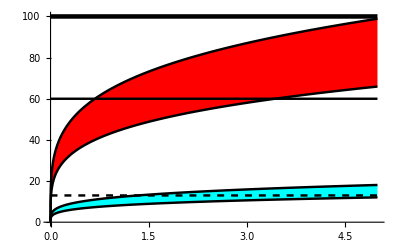

```mathematica
fig3b= Show[figx1,figx2,PlotRange-> {All, {0,Automatic}},AxesStyle->as, PlotRangePadding->None]
```

### panel C

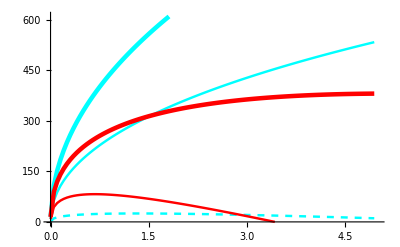

```mathematica
a1 = 1; b1 = 0.75; a2 = 5 a1; b2  = 0.75;  a3 = 1 ;
allabparam = {a1, b1, a2,b2, a3, b3};
AB= {{a1, b1, a2,b2, a3, 0.5},{a1, b1, a2,b2, a3, 0.8},{a1, b1, a2,b2, a3, 1.25}};
cTmax = 0.;
nowarmup = True;
free = True;
aw = 0.;

fe[z_,Trise_,ε_ ]:=EnTime[z, trise,Trise, Trise +cTmax,ε, trise,tf,allabparam, nowarmup,free ,aw];

nstep = 100;

data1 = Table[Flatten@{z,fe[z,Trise1, eps[[1]]]},{z,0.001,5.,5/nstep}];
data2 = Table[Flatten@{z,fe[z,Trise1,eps[[2]]]},{z,0.001,5.,5/nstep}];
data3 = Table[Flatten@{z,fe[z,Trise1, eps[[3]]]},{z,0.001,5.,5/nstep}];
data4 = Table[Flatten@{z,fe[z,Trise2, eps[[1]]]},{z,0.001,5.,5/nstep}];
data5 = Table[Flatten@{z,fe[z,Trise2, eps[[2]]]},{z,0.001,5.,5/nstep}];
data6 = Table[Flatten@{z,fe[z,Trise2, eps[[3]]]},{z,0.001,5.,5/nstep}];

pse = {{AbsoluteThickness[th],Dashed, Cyan},{AbsoluteThickness[th], Cyan},{AbsoluteThickness[th+1.5], Cyan},{AbsoluteThickness[th],Dashed, Red},{AbsoluteThickness[th], Red},{AbsoluteThickness[th+1.5], Red}};

fig3c = ListLinePlot[{data1,data2,data3,data4,data5,data6},PlotRange->{{0,5},{0,610}},AxesOrigin-> {0,0},PlotStyle->pse,AxesStyle-> as,PlotRangePadding->None]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\final_energy_budget\\energy_budget\\ms_fig\\Figure2\\fig2a.jpg",fig2a,ImageResolution->200];
Export["C:\\Users\\tramiada\\Documents\\Projects\\final_energy_budget\\energy_budget\\ms_fig\\Figure2\\fig2b.jpg",fig2b,ImageResolution->200];
Export["C:\\Users\\tramiada\\Documents\\Projects\\final_energy_budget\\energy_budget\\ms_fig\\Figure2\\fig2c.jpg",fig2c,ImageResolution->200];
```

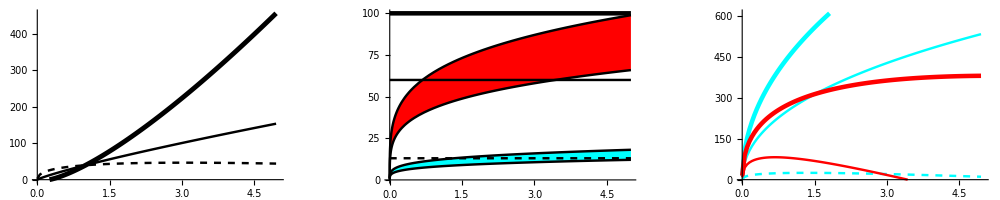

```mathematica
fig3 = GraphicsRow[{fig3a,fig3b,fig3c},Spacings-> {70,0},ImageSize-> 1000]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\final_energy_budget\\energy_budget\\ms_fig\\fig3.pdf",fig3]
```

C:\Users\tramiada\Documents\Projects\final_energy_budget\energy_budget\ms_fig\fig3.pdf

## Figure 4

### panel A: cSR = 0.25, aw = 0, K1 = 0.1 free convection

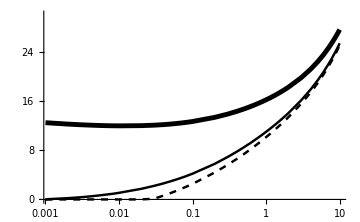

```mathematica
cSR = 0.25; aw = 0.; rK1 = 0.1;free = True;

SR  = #/(6*3600) *cSR 1320. &;
Te = #2 + 0 #1/(6*3600.) &;  

(*this function is for the change in thoracic (and surface) temperature *)
changeTthEndo[z_, rK1_, rK2_,minT_,free_,aw_]:= Module[{maxt = 6*3600, ε= 0.95, r3 =0.5,sol, cz = fcz[z]},
Assert[cz<0.75];
sol = If[free == True,
NDSolve[
{ Tth'[t] == 1/(s cz z ) (aw * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz)z) *( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  0.05 Max[0.,(Ts[t]- Te[t,minT])]^(1.25) (1/(z/δ))^(1/12) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,minT])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==minT},{Tth,Ts},{t,0,maxt}],
NDSolve[
{Tth'[t] == 1/(s cz z) (aw * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz) z) * ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (Ts[t]- Te[t,minT]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,minT])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==minT},{Tth,Ts},{t,0,maxt}]
];
sol];

(*This finds an interval of temperature such that at maxt, f(T1) < Tw and f(T2)>Tw, the condition is that Abs[f(t1) - f(t2)] < 0.01*)
findTminEndo[z_, rK1_, rK2_, free_,aw_]:=Module[{Tw = 28 + 1. 0.75 z,T1,T2, Tmid,maxt = 6*3600,Tf1,Tf2,sol,Tfmid},
T1 = 0;
T2 = 100;
Tf1 = 0;
Tf2 = 100; 
Tmid = T1;

sol  = changeTthEndo[z,rK1, rK2, T1, free,aw];
Tf1 = Tth[maxt]/.sol[[1]];
If[Tf1 > Tw, Goto[end]];

While[Abs[Tf1 -Tf2] > 10^(-2),
Tmid = T1 + (T2 - T1 )/2;

sol  = changeTthEndo[z,rK1, rK2, Tmid, free,aw];
Tfmid = Tth[maxt]/.sol[[1]];

Which[
Tfmid < Tw,Tf1 = Tfmid;T1 = Tmid,
Tfmid > Tw,Tf2 = Tfmid;T2 = Tmid,
Tfmid == Tw,T1 = Tmid;Goto[end] 
];
];
Label[end];
N@{z,T1}];

vect = Flatten[{Range[0.001,0.01,0.001],Range[0.02,0.1,0.01],Range[0.2,2,0.1],Range[3,10,1]}];

data= Table[Table[findTminEndo[z,rK1,rK2,free,aw], {z, vect}],{rK2,{0.1,1,10}}];

fig4a = ListLogLinearPlot[data,Joined->True,PlotRange-> {All, {0,30}},PlotStyle->ps,AxesStyle->as,ImageSize->Medium, PlotRangePadding->0.1]
```

### panel B: cSR = 0.25, aw = 0, K1 = 1, laminar convection

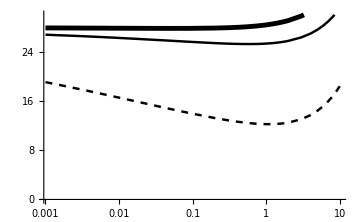

```mathematica
cSR = 0.25; aw = 0.; rK1 = 1.; free = False;

SR  = #/(6*3600) *cSR 1320. &;
Te = #2 + 0 #1/(6*3600.) &;  

(*this function is for the change in thoracic (and surface) temperature *)
changeTthEndo[z_, rK1_, rK2_,minT_,free_,aw_]:= Module[{maxt = 6*3600, ε= 0.95, r3 =0.5,sol, cz = fcz[z]},
Assert[cz<0.75];
sol = If[free == True,
NDSolve[
{ Tth'[t] == 1/(s cz z ) (aw * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz)z) *( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  0.05 Max[0.,(Ts[t]- Te[t,minT])]^(1.25) (1/(z/δ))^(1/12) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,minT])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==minT},{Tth,Ts},{t,0,maxt}],
NDSolve[
{Tth'[t] == 1/(s cz z) (aw * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz) z) * ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (Ts[t]- Te[t,minT]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,minT])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==minT},{Tth,Ts},{t,0,maxt}]
];
sol];

(*This finds an interval of temperature such that at maxt, f(T1) < Tw and f(T2)>Tw, the condition is that Abs[f(t1) - f(t2)] < 0.01*)
findTminEndo[z_, rK1_, rK2_, free_,aw_]:=Module[{Tw = 28 + 1. 0.75 z,T1,T2, Tmid,maxt = 6*3600,Tf1,Tf2,sol,Tfmid},
T1 = 0;
T2 = 100;
Tf1 = 0;
Tf2 = 100; 
Tmid = T1;

sol  = changeTthEndo[z,rK1, rK2, T1, free,aw];
Tf1 = Tth[maxt]/.sol[[1]];
If[Tf1 > Tw, Goto[end]];

While[Abs[Tf1 -Tf2] > 10^(-2),
Tmid = T1 + (T2 - T1 )/2;

sol  = changeTthEndo[z,rK1, rK2, Tmid, free,aw];
Tfmid = Tth[maxt]/.sol[[1]];

Which[
Tfmid < Tw,Tf1 = Tfmid;T1 = Tmid,
Tfmid > Tw,Tf2 = Tfmid;T2 = Tmid,
Tfmid == Tw,T1 = Tmid;Goto[end] 
];
];
Label[end];
N@{z,T1}];

vect = Flatten[{Range[0.001,0.01,0.001],Range[0.02,0.1,0.01],Range[0.2,2,0.1],Range[3,10,1]}];

data= Table[Table[findTminEndo[z,rK1,rK2,free,aw], {z, vect}],{rK2,{0.1,1,10}}];

fig4b = ListLogLinearPlot[data,Joined->True,PlotRange-> {All, {0.001,30}},PlotStyle->ps,AxesStyle->as,ImageSize->Medium, PlotRangePadding->0.1]
```

### panel C: cSR = 0.25, aw = 1.25, K1 = 1, laminar convection

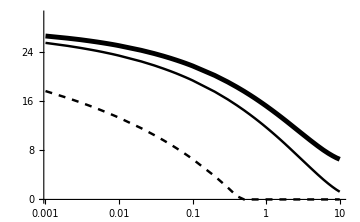

```mathematica
cSR = 0.25; aw = 1.25; rK1 = 1.; free = False;

SR  = #/(6*3600) *cSR 1320. &;
Te = #2 + 0 #1/(6*3600.) &;  

(*this function is for the change in thoracic (and surface) temperature *)
changeTthEndo[z_, rK1_, rK2_,minT_,free_,aw_]:= Module[{maxt = 6*3600, ε= 0.95, r3 =0.5,sol, cz = fcz[z]},
Assert[cz<0.75];
sol = If[free == True,
NDSolve[
{ Tth'[t] == 1/(s cz z ) (aw * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz)z) *( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  0.05 Max[0.,(Ts[t]- Te[t,minT])]^(1.25) (1/(z/δ))^(1/12) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,minT])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==minT},{Tth,Ts},{t,0,maxt}],
NDSolve[
{Tth'[t] == 1/(s cz z) (aw * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz) z) * ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (Ts[t]- Te[t,minT]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,minT])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==minT},{Tth,Ts},{t,0,maxt}]
];
sol];

(*This finds an interval of temperature such that at maxt, f(T1) < Tw and f(T2)>Tw, the condition is that Abs[f(t1) - f(t2)] < 0.01*)
findTminEndo[z_, rK1_, rK2_, free_,aw_]:=Module[{Tw = 28 + 1. 0.75 z,T1,T2, Tmid,maxt = 6*3600,Tf1,Tf2,sol,Tfmid},
T1 = 0;
T2 = 100;
Tf1 = 0;
Tf2 = 100; 
Tmid = T1;

sol  = changeTthEndo[z,rK1, rK2, T1, free,aw];
Tf1 = Tth[maxt]/.sol[[1]];
If[Tf1 > Tw, Goto[end]];

While[Abs[Tf1 -Tf2] > 10^(-2),
Tmid = T1 + (T2 - T1 )/2;

sol  = changeTthEndo[z,rK1, rK2, Tmid, free,aw];
Tfmid = Tth[maxt]/.sol[[1]];

Which[
Tfmid < Tw,Tf1 = Tfmid;T1 = Tmid,
Tfmid > Tw,Tf2 = Tfmid;T2 = Tmid,
Tfmid == Tw,T1 = Tmid;Goto[end] 
];
];
Label[end];
N@{z,T1}];


vect = Flatten[{Range[0.001,0.01,0.001],Range[0.02,0.1,0.01],Range[0.2,2,0.1],Range[3,10,1]}];


data= Table[Table[findTminEndo[z,rK1,rK2,free,aw], {z, vect}],{rK2,{0.1,1,10}}];

fig4c= ListLogLinearPlot[data,Joined->True,PlotRange-> {All, {0,30}},PlotStyle->ps,AxesStyle->as,ImageSize->Medium, PlotRangePadding->0.1]
```

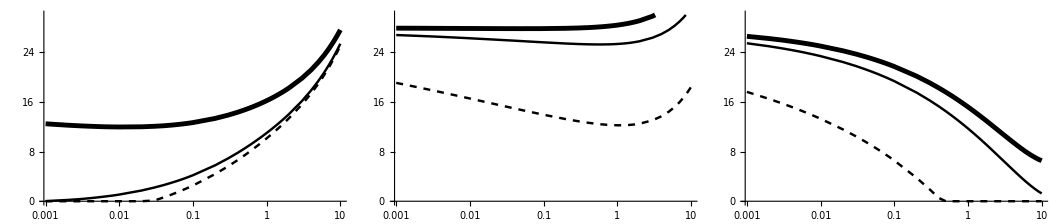

```mathematica
fig4 = GraphicsGrid[{{fig4a,fig4b,fig4c}},Spacings->-10]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\final_energy_budget\\energy_budget\\ms_fig\\fig4.pdf",fig4]
```

C:\Users\tramiada\Documents\Projects\final_energy_budget\energy_budget\ms_fig\fig4.pdf

## Figure 5

### Additional code

```mathematica
On[Assert];

(*Position of the sun in the sky as a function of day of the year, time of the day, and latitude at longitude = 0*)
SolarRadiation[J_,t_,ϕ_]:= Module[{result,S0=1.361,sinδ,δ,cosδ, cosψ,sol,trise,tset,tt, DtoR = π/180,hs},
sinδ = 0.39785 Sin[(278.97 + 0.9856 J + 1.9165 Sin[(356.6 + 0.9856 J)DtoR])DtoR];
(*this is solar declination*)
δ = ArcSin[sinδ];
cosδ = Cos[δ];
cosψ[ti_]:=Sin[ϕ DtoR]sinδ + Cos[ϕ DtoR] cosδ Cos[(15.(ti-12))DtoR];

hs[δ_]:= ArcCos[(0 - Sin[ϕ DtoR]sinδ)/(Cos[ϕ DtoR] cosδ)]1/DtoR; 
(*cosψ disapears because we use geometric sunset*)
trise = 12- hs[δ]/15;
tset = 12 + hs[δ]/15;

If[t< trise || t > tset, 
result = 0,
result = S0 cosψ[t];
];
result *= 1000;
result];

(*Position of the sun in the sky as a function of day of the year, time of the day, and latitude at longitude = 0*)
SunRise[J_,ϕ_]:= Module[{result,sinδ,δ,cosδ, cosψ,sol,trise,tset,tt, DtoR = π/180,hs},
sinδ = 0.39785 Sin[(278.97 + 0.9856 J + 1.9165 Sin[(356.6 + 0.9856 J)DtoR])DtoR];
(*this is solar declination*)
δ = ArcSin[sinδ];
cosδ = Cos[δ];

hs[δ_]:= ArcCos[(0 - Sin[ϕ DtoR]sinδ)/(Cos[ϕ DtoR] cosδ)]1/DtoR; 
(*cosψ disapears because we use geometric sunset*)
trise = 12- hs[δ]/15;
result= Re@trise;
result];

(*Fixed constant and solar radiation function *)
day = 72 +0 91; lat = 30;
trise = SunRise[day,lat];ZZ= {0.01,0.1,1,10};

(* data for solar radiation *)
predata = Table[{t, SolarRadiation[day,t,lat]},{t, trise,trise+12,12/10}];
SR = Interpolation[predata];

(*CONSTANTS AND SIMPLE FUNCTIONS USED*)

c0= 28.;
c1 = 1.5;
cz = 0.5;

(*Convection*)
cp =29.3; (*J/ mol K*)
wind = 1; (*m/s*)
(*original data tissue density:
1 kg /l =  1 kg/dm^3 = 1000g/dm^3 = 1000 g/ 10^(-3) m^3  = 1 10^6 g/m^3
*)
δ = 0.15 10^(6);(*measurement gives the 0.15. g/m^3*)
Ksth =0.05* cp (*this is tissue conductance. A sleeping bag has 0.05 (ex #6.4, mol / m2 s * J / mol K  *);

s = 3.3472 ;(*specific heat capacity, 0.8 cal /g C = 0.8*4.184 J/g C*)
σ=5.67 10^(-8);(*W/m2 K4 = J / m2 s K*)
e = 0.04184;(*energy per contraction: 0.01 cal/g = 0.01*4.184 j/g*)

rK1 = 1; (* Coefficient for the conductance between the thorax and the rest of the body *)
rK2 = 1; (* Coefficient for the convection between the thorax and the environment *)
free = 0; (* Binary value 0 or 1 where there is free convection or laminar convection*)

Kv[z_]:= cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (* J/mol K x mol /m2 s = J / m2 K s*);

aw = 0.25; (*something per second*)
f[T_]:= aw T;

rad[z_]:= (3. z/(2 π δ))^(1/3);

Ath[z_]:= 2 π rad[z]^2;
As[z_]:= 3 π rad[z]^2;
fcz[z_]:= 0.5;

(*function for changes in environmental temperature*)
fTemp[t_,trise_,Trise_,Tmax_]:= Module[{tmax,tset,Tnoon,Tset,cT = 0.5,result},

If[
Trise == Tmax,result = Trise;Goto["end"]
];
Assert[Tmax >Trise];

tmax = 12 + 0.5 (12 - trise);
tset = 12 + (12- trise);
Tnoon  = Trise - (Tmax- Trise)/(tmax - trise) trise+ (Tmax- Trise)/(tmax - trise) 12;
Tset = Tnoon + cT (Tmax - Tnoon);

result = 
Which[
trise≤ t< tmax,
 Trise - (Tmax- Trise)/(tmax - trise) trise+ (Tmax- Trise)/(tmax - trise) t,
tmax ≤ t< tset,
 Tmax - (Tset- Tmax)/(tset - tmax) tmax+ (Tset- Tmax)/(tset - tmax) t,
tset ≤ t< trise +24,
 Tset  - (Trise - Tset)/(trise +24  - tset) tset + (Trise - Tset)/(trise +24  - tset)t
];

Label["end"];

result];

(*this function solve the the change in thoracic (and surface) temperature and find the warm-up time *)
Wtime[z_, rK1_, rK2_,starttf_,endtf_,free_, trise_, Trise_, Tmax_,aw_]:= Module[{ ε= 0.95, r3 =0.5,sol, cz = fcz[z], T1 , xy,pos,result, activetemp = c0 + c1 z cz ,Temp, newendtf, yy,maxyy,t1,t2,yt1,yt2,tmid,ytmid},

Temp[t_]:= fTemp[t,trise,Trise, Trise + Tmax ]; (*Simplify the definition of changes in temperature*)

T1 = Temp[starttf];
Assert[NumericQ@T1 == True];
newendtf = Min[endtf,12  +  (12 -trise)];

If[T1 ≥ activetemp, result = 0.; Goto[end]];

sol = If[free == True,
NDSolve[
{ Tth'[t] == 1/(s cz z ) (aw * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz)z) *( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  0.05 Max[0.,(Ts[t]- Temp[t/3600.])]^(1.25) (1/(z/δ))^(1/12) - σ ε (273 + Ts[t])^4 + σ ε (273 + Temp[t/3600.])^4 + r3 SR[t/3600.])) ,Tth[starttf *3600.]==Ts[starttf *3600.]==T1},{Tth,Ts},{t,starttf *3600., newendtf* 3600.}],
NDSolve[
{Tth'[t] == 1/(s cz z) (aw * cz z e   +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s (1-cz) z) * ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2  cp 1.4 0.135 Sqrt[wind/(z/δ)^(1/3)] (Ts[t]- Temp[t/3600.]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Temp[t/3600.])^4 + r3 SR[t/3600.])) ,Tth[starttf *3600.]==Ts[starttf *3600.]==T1},{Tth,Ts},{t,starttf *3600., newendtf* 3600.}]
];


(* Compute all values *)
yy = Table[Evaluate[Re@Tth[t]/.sol],{t,starttf*3600,newendtf*3600,2}];
maxyy = Max[yy];

If[maxyy < activetemp,
result = endtf -starttf,
pos = Position[yy,maxyy][[1,1]];
t1 = starttf*3600;
t2 = t1 + 2(pos-1); (*The minus one occurs because imagine max is at starttf, time 2 because of discretization in yy*)
yt1 = Evaluate[Re@Tth[t1] /. sol][[1]] - activetemp;
yt2 = Evaluate[Re@Tth[t2] /. sol][[1]] -activetemp;
Assert[yt1*yt2 < 0];
While[Abs[yt1 -yt2] > 10^(-5),
tmid = t1 + (t2 -t1)/2;
ytmid = Evaluate[Re@Tth[tmid] /. sol][[1]] - activetemp;
If[ytmid < 0,
t1 = tmid;
yt1 = ytmid,
t2 = tmid;
yt2 = ytmid
];
];
result = (t1 + t2)/(2. 3600) - starttf;
];
Label[end];
result];
```

### panel A

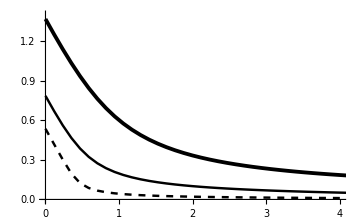

```mathematica
ZZ= {0.01,1,10};

Trise = 15; Tmax= 15;
trise = SunRise[day,lat];
free = True;
rK2 = 1; rK1 = 1;
aw= 0;

endtf= 16 ;

data1 = Table[Table[{delay,Wtime[z, rK1,rK2,trise+ delay,endtf,free, trise, Trise,Tmax,aw]},{delay,0,12- trise,(12-trise)/50}],{z,ZZ}];

ps = Reverse@{{Black,AbsoluteThickness[th+2]}, {Black,AbsoluteThickness[th+1]}, {Black,AbsoluteThickness[th]},{Black,Dashed, AbsoluteThickness[th]}};

fig5a = ListPlot[data1,Joined->True,PlotRange-> {{0,4(*12-trise*)}, {0,1.4}},PlotStyle-> ps,AxesStyle->as,ImageSize->Medium,PlotRangePadding->None]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\final_energy_budget\\energy_budget\\ms_fig\\Figure4\\fig4a.jpg",fig4a,ImageResolution->200];
```

### panel B

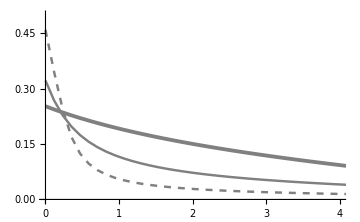

```mathematica
Trise = 15; Tmax= 15;
trise = SunRise[day,lat];
free = True;
rK2 =  1; 
z=1.;
aw= 1.25;

endtf= 16 ;

data1 = Table[Table[{delay,Wtime[z, rK1,rK2,trise+ delay,endtf,free, trise, Trise,Tmax,aw]},{delay,0,12- trise,(12-trise)/50}],{rK1,{0.1,1,10}}];

ps ={{Gray,AbsoluteThickness[th+1]}, {Gray,AbsoluteThickness[th]},{Gray,Dashed, AbsoluteThickness[th]}};

fig5b = ListPlot[data1,Joined->True,PlotRange-> {{0,4(*12-trise*)}, {0,0.5}},PlotStyle-> ps,AxesStyle->as,ImageSize->Medium,PlotRangePadding->None]
```

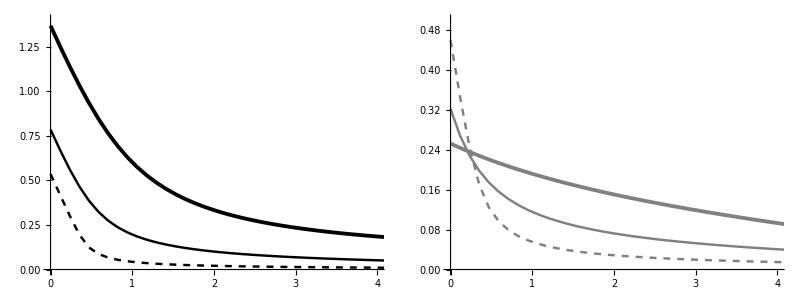

```mathematica
fig5 = Grid[{{fig5a,fig5b}},Spacings->{5,0}]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\final_energy_budget\\energy_budget\\ms_fig\\fig5.pdf",fig5];
```

## Figure 6

### panel A

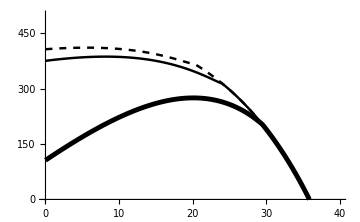

```mathematica
a1 = 1; b1 = 0.75; a2 = 10 a1; b2  = 0.75;  a3 = 1; b3 = 0.75 ;
allabparam = {a1, b1, a2,b2, a3, b3};
AB  = Table[{a1, b1, a2,b2, a3, b3},{b3,{0.5,1, 1.25}}];
ε = 30;
cTmax = 0.;
RR =30.;
nowarmup = False;
free = True;
aw = 1.25;

tf = 1;
zz = 2;
TRISE= {trise, trise +2, trise +4};

f2[Trise_,i_]:=EnTime[zz, trise,Trise, Trise +cTmax,ε, TRISE[[i]],tf,allabparam, False,True,aw];

step = 0.5;
(*data1 = Table[Flatten@{temp,f[temp,1]},{temp,0,40,step}];*)
data2 = Table[Flatten@{temp,f2[temp,1]},{temp,0,40,step}];
data3 = Table[Flatten@{temp,f2[temp,2]},{temp,0,40,step}];
data4 = Table[Flatten@{temp,f2[temp,3]},{temp,0,40,step}];

fig6a = ListLinePlot[{(*data1,*)data4,data3,data2},PlotRange->{{0,40},{0,500}},AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,ImageSize->Medium,PlotRangePadding->None]
```

```mathematica
trise
```

6.12682

### panel B

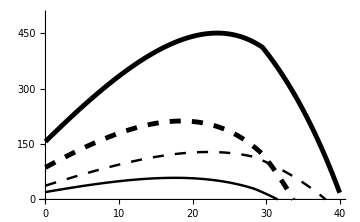

```mathematica
a1 = 1; b1 = 0.75; a2 = 10 a1; b2  = 0.75;  a3 = 1; b3 = 0.5 ;
allabparam = {a1, b1, a2,b2, a3, b3};
AB  = Table[{a1, b1, a2,b2, a3, b3},{b3,{0.5, 1.25}}];
ε = 30;
cTmax = 0.;
RR =30.;
nowarmup = False;
free = True;
aw = 1.25;

tf = 1;
zz2 = 2;
zz1= 0.5;

ps = {{AbsoluteDashing[{8,8}], AbsoluteThickness[th],Black},{AbsoluteThickness[th ],Black},{Black,AbsoluteDashing[{8,8}],AbsoluteThickness[2th]},{Black,AbsoluteThickness[2 th]}};

f[Trise_,i_, zz_]:=EnTime[zz, trise,Trise, Trise +cTmax,ε, trise,tf,AB[[i]], False,True,aw];

step = 0.5;
data1 = Table[Flatten@{temp,f[temp,1,zz1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,f[temp,2, zz1]},{temp,0,40,step}];
data3 = Table[Flatten@{temp,f[temp,1, zz2]},{temp,0,40,step}];
data4 = Table[Flatten@{temp,f[temp,2,zz2]},{temp,0,40,step}];

fig6b = ListLinePlot[{data1,data2,data3,data4},PlotRange->{{0,40},{0,500}},ImageSize->Medium,AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None]
```

### panel C

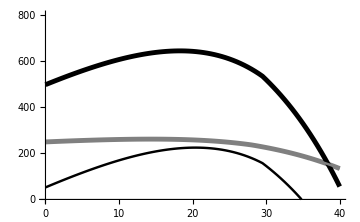

```mathematica
a1 = 1; b1 = 0.75; a2 = 10 a1; b2  = 0.75;  a3 = 1; b3 = 0.75 ;
allabparam = {a1, b1, a2,b2, a3, b3};
ε = 30;
cTmax = 0.;
RR =30.;
nowarmup = False;
free = True;
aw = 1.25;
ZZ = {0.1,2};
TF1 = Table[Min[ftf[ZZ[[i]],RR,a3,b3],ftf[ZZ[[i]],ZZ[[i]]*100,a3,b3]],{i,2}];
TF2 = Table[Min[ftf[ZZ[[i]],RR/2,a3,b3],ftf[ZZ[[i]],ZZ[[i]]*100,a3,b3]],{i,2}];

f1[Trise_,i_]:=EnTime[ZZ[[i]], trise,Trise, Trise +cTmax,ε, trise,TF1[[i]],allabparam, False,True,aw];
f2[Trise_,i_]:=EnTime[ZZ[[i]], trise,Trise, Trise +cTmax,ε, trise,TF2[[i]],allabparam, False,True,aw];

step = 0.5;
data1 = Table[Flatten@{temp,f1[temp,1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,f1[temp,2]},{temp,0,40,step}];
data3 = Table[Flatten@{temp,f2[temp,1]},{temp,0,40,step}];
data4 = Table[Flatten@{temp,f2[temp,2]},{temp,0,40,step}];

 ps = {{Gray,AbsoluteThickness[2th]},{Black,AbsoluteThickness[2 th]},{Gray,AbsoluteThickness[th]},{Black,AbsoluteThickness[th]}};

fig6c = ListLinePlot[{data1,data2,data3,data4},PlotRange->{{0,40},{0,800}},ImageSize->Medium,AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None]
```

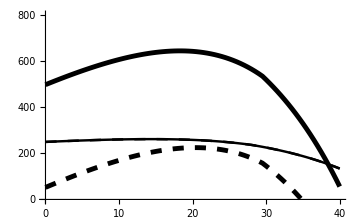

```mathematica
ps = {{AbsoluteThickness[th],Black},{Black,AbsoluteThickness[2 th]},{AbsoluteDashing[{8,8}],Black,AbsoluteThickness[th]},{AbsoluteDashing[{8,8}],Black,AbsoluteThickness[2 th]}};

fig6c = ListLinePlot[{data1,data2,data3,data4},PlotRange->{{0,40},{0,800}},ImageSize->Medium,AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None]
```

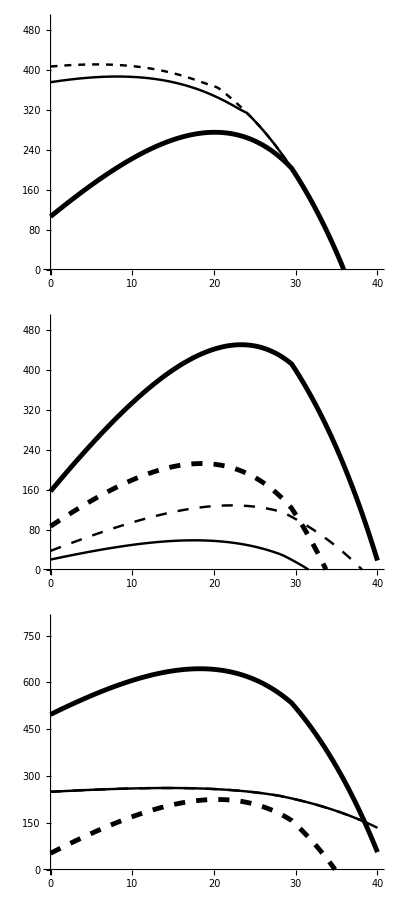

```mathematica
fig6 = Grid[Transpose@{{fig6a,fig6b,fig6c}},Spacings->{1,5}]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\final_energy_budget\\energy_budget\\ms_fig\\fig6.pdf",fig6];
```